```mathematica
Normalize[{2,2}]
```

{1/(√2),1/(√2)}

```mathematica
ccw90[p_]:={p[[2]],-p[[1]]}
cw90[p_]:={-p[[2]],p[[1]]}
```

```mathematica
capsule[a_,b_,r_]:=(
 diff=b-a;
 u=Normalize[ccw90[diff]]*r;
d=Normalize[cw90[diff]]*r;
aUp=a+u;
aDown=a+d;
bUp=b+u;
bDown=b+d;
{Circle[a,r],Line[{aUp,bUp}],Line[{aDown,bDown}],Circle[b,r]}
)
```

```mathematica
stroke17={6.875,6.375};
stroke18={7.21875,7.0};
stroke20={7.96875,7.9375};
stroke21={8.34375,8.1875};
```

enters at 17.48290604935480397
exits at 17.0.9075077419106311
exits at 20.7889052396611623

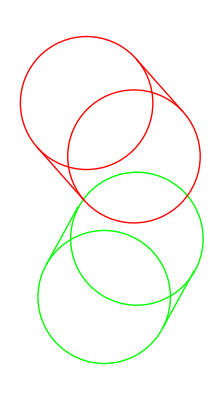

```mathematica
Graphics[{Green,capsule[stroke17,stroke18,Sqrt[0.5]],Blue,Point[stroke17+48290604935480397(stroke18-stroke17)],Point[stroke17+48290604935480397(stroke18-stroke17)],Red,capsule[{6.6875,8.4375},{7.1875,7.875},Sqrt[0.5]]}]
```